```mathematica
map1=Rasterize[Graphics[{Antialiasing->False,Black,Thickness[0.05],Line[{{1,1},{20,1},{20,20},{1,20},{1,1}}],
Line[{{1,5},{20,10}}],
Line[{{1,6},{20,11}}]
}],RasterSize->{20,20}];
map1=(map1/.Graphics->List)[[1,1]]/.{{0,0,0}->1,{255,255,255}->0};
map1[[4,2]]=2;
map1[[15,15]]=3;
```

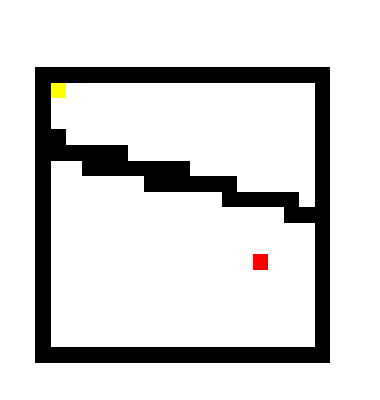

```mathematica
ArrayPlot[map1,ColorRules->{0->White,1->Black,2->Yellow,3->Red}]
```

```mathematica
Export["map1.csv",map1]
```

map1.csv

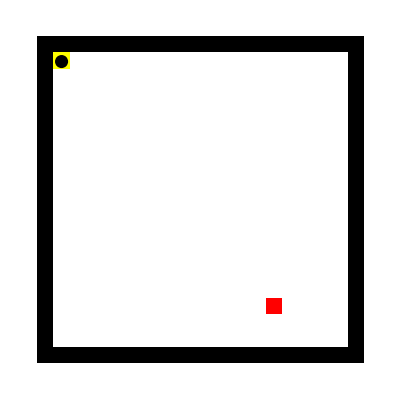

```mathematica
map2=Import["~/java/ne/map1.csv"];
Show[ArrayPlot[map2,ColorRules->{0->White,1->Black,2->Yellow,3->Red},DataRange->{{1,20},{1,20}},PlotRangePadding->None,Frame->False,ImagePadding->None,PlotRangeClipping->True],
Graphics[{Disk[{2,19},0.4]}]]
```

```mathematica
Needs["ExperimentEvaluation`"]
```

```mathematica
data=readAllFiles[{"MAZE"}];
```

```mathematica
printAsTable[data,{"SOLVER"}]
```

ID | PARAM FILE | SOLVER
1 | MAZE/parameters_001.txt | GPAT

```mathematica
expr=sortConfigurationResults[data,"1","BSF",1,Output->"BSF"][[1,4,1]]
```

plus[1.01639 atan[plus[-2.10364 times[x1,x3],-0.718324 x5]],3.85049 x1]

```mathematica
neighbours[state_]:=
Module[{pos=OptionValue[state,pos],map=OptionValue[state,map],dir=OptionValue[state,dir],nr},
nr=map[[pos[[1]]-1;;pos[[1]]+1,pos[[2]]-1;;pos[[2]]+1]];
Switch[dir,
"N",nr,
"W",{nr[[All,3]],nr[[All,2]],nr[[All,1]]},
"E",{{nr[[1,3]],nr[[2,3]],nr[[3,3]]},{nr[[1,2]],nr[[2,2]],nr[[3,2]]},{nr[[1,1]],nr[[1,2]],nr[[1,3]]}},
"S",{{nr[[3,3]],nr[[3,2]],nr[[3,1]]},{nr[[2,3]],nr[[2,2]],nr[[2,1]]},{nr[[1,3]],nr[[1,2]],nr[[1,1]]}}
]
]
```

```mathematica
rotateR[state_]:=
Module[{dirs={"N","E","S","W"}},
moveF@(state/.(dir->_)->
(dir->(RotateLeft[dirs])[[Position[dirs,OptionValue[state,dir]][[1,1]]]]))
]
```

```mathematica
rotateL[state_]:=
Module[{dirs={"N","E","S","W"}},
moveF@(state/.(dir->_)->
(dir->(RotateRight[dirs])[[Position[dirs,OptionValue[state,dir]][[1,1]]]]))
]
```

```mathematica
moveF[state_]:=
Module[{p=OptionValue[state,pos],dir=OptionValue[state,dir],,r=OptionValue[state,dir],newPos},
newPos=Switch[dir,
"N",{p[[1]]-1,p[[2]]},
"W",{p[[1]],p[[2]]-1},
"S",{p[[1]]+1,p[[2]]},
"E",{p[[1]],p[[2]]+1}
];
If[neighbours[state][[1,2]]≠1,
state/.{(pos->_)->(pos->newPos),(route->old:_)->(route->(old~Join~{newPos}))},
,state
]
]
```

```mathematica
inputVector[state_]:=
Module[{pos=OptionValue[state,pos],target=OptionValue[state,target],map=OptionValue[state,map],dir=OptionValue[state,dir],n,slice},
n=neighbours[state];
Switch[dir,
"N",slice={pos[[1]]≥target[[1]],pos[[1]]≤target[[1]],pos[[2]]≥target[[2]],pos[[2]]≤target[[2]]},
"S",slice={pos[[1]]≤target[[1]],pos[[1]]≥target[[1]],pos[[2]]≤ target[[2]],pos[[2]]≥target[[2]]},
"W",slice={pos[[2]]≥target[[2]],pos[[2]]≤target[[2]],pos[[1]]≤target[[1]],pos[[1]]≥target[[1]]},
"E",slice={pos[[2]]≤target[[2]],pos[[2]]≥target[[2]],pos[[1]]≥target[[1]],pos[[1]]≤target[[1]]}
];
{1.0,
If[n[[1,1]]==1,1.0,0.0],
If[n[[1,2]]==1,1.0,0.0],
If[n[[1,3]]==1,1.0,0.0],
Sequence@@(slice/.{True->1.0,False->0.0})
}
]
```

```mathematica
showState[state_]:=
Module[{pos=OptionValue[state,pos],map=OptionValue[state,map],dir=OptionValue[state,dir],route=OptionValue[state,route],p},
route={#[[2]],Length[map]-#[[1]]+1}&/@route;
p={pos[[2]],Length[map]-pos[[1]]+1};
Show[
ArrayPlot[map,ColorRules->{0->White,1->Black,2->Yellow,3->Red},DataRange->{{1,Length[map]},{1,Length[map]}},PlotRangePadding->None,Frame->False,ImagePadding->None,PlotRangeClipping->True,Mesh->True],
Graphics[{Line[route],Disk[p,0.4]}]
]
]
```

```mathematica
state={pos->Flatten[Position[map2,2]],target->Flatten[Position[map2,3]],dir->"S",map->map2,route->{Flatten[Position[map2,2]]}};
```

```mathematica
state
```

{pos→{2,2},target→{17,15},dir→S,map→{{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},{1,2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1},{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1},{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1},{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1},{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1},{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1},{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1},{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1},{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1},{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1},{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1},{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1},{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1},{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1},{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1},{1,0,0,0,0,0,0,0,0,0,0,0,0,0,3,0,0,0,0,1},{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1},{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1},{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}},route→{{2,2}}}

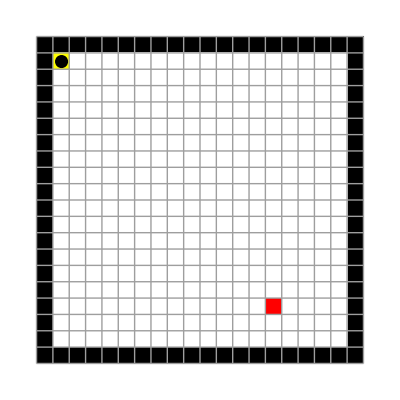

```mathematica
showState[state]
```

```mathematica
inputVector[state]
```

{1.,0.,0.,1.,1.,0.,1.,0.}